```mathematica
(* zadachaaaa 1 *)
```

```mathematica
xs = {2,4,6,7,10,11,14,17,20}
ys = {4,5,6,7,8,8,11,10,12}
```

{2,4,6,7,10,11,14,17,20}

{4,5,6,7,8,8,11,10,12}

```mathematica
dots = {};
For[i=1,i≤Length[xs],i++,
AppendTo[dots,{xs[[i]],ys[[i]]}]
]
```

```mathematica
f[x_] = a *x +b;
```

```mathematica
sum[a_,b_] = ∑_(i=1)^Length[xs] (f[xs[[i]]] - ys[[i]])^2//Expand
```

619-1690 a+1211 a^2-142 b+182 a b+9 b^2

```mathematica
solve = NSolve[{D[sum[a,b], a] ==0,D[sum[a,b], b] ==0},{a,b}]
```

{{a→0.436975,b→3.47059}}

```mathematica
f[x_] = f[x]/. solve[[1]]
```

3.47059+0.436975 x

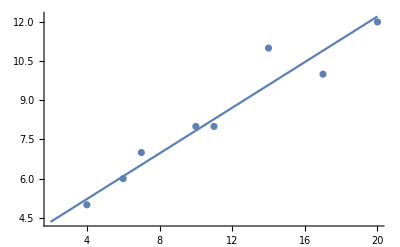

```mathematica
listDots = ListPlot[dots];
plot = Plot[f[x],{x,xs[[1]],xs[[Length[xs]]]}];
Show[plot,listDots]
```

```mathematica
(* zadacha 2 *)
```

```mathematica
fs = { x+2y, x-y, 3x+4y};
yses = {1,5,17};

sum[x_,y_] = ∑_(i=1)^Length[yses] (fs[[i]] - yses[[i]])^2 //Expand
```

315-114 x+11 x^2-130 y+26 x y+21 y^2

```mathematica
solve = NSolve[{D[sum[x,y], x] == 0,D[sum[x,y], y] == 0},{x,y}]
```

{{x→5.67742,y→-0.419355}}

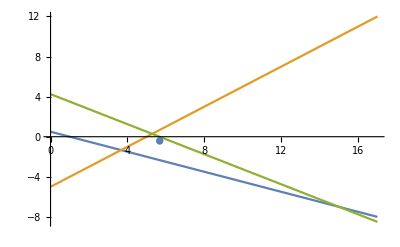

```mathematica
plot = Plot[{(1-x)/2,x-5,(17-3x)/4},{x,0,17}];
dot = ListPlot[{{5.677419354838707,-0.4193548387096758}}];
Show[plot,dot]
```

```mathematica
(* zadacha 3 *)
```

```mathematica
weight=1;
F[x_] = Sin[x];
P[x_] = a*x^2+b*x +c;
```

```mathematica
avQadAppr[a_,b_,c_] = ∫_0^(π/2) weight*(F[x] - P[x])^2 ⅆx
```

4 a-2 c-2 (b+a π)+1/480 π (120+240 c^2+20 b^2 π^2+15 a b π^3+3 a^2 π^4+40 c π (3 b+a π))

```mathematica
coefs = NSolve[{D[avQadAppr[a,b,c], a] ==0,D[avQadAppr[a,b,c], c] ==0,D[avQadAppr[a,b,c], b] ==0},{a,b,c}]
```

{{a→-0.33824,b→1.19575,c→-0.0243249}}

```mathematica
P[x_] = P[x]/.coefs[[1]]
```

-0.0243249+1.19575 x-0.33824 x^2

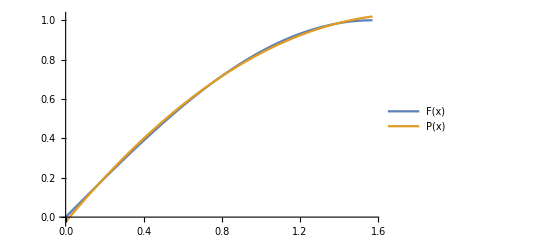

```mathematica
Plot[{F[x],P[x]},{x,0,Pi/2},PlotLegends->"Expressions"]
```

```mathematica
(* ravnomerno razstonie *)
```

```mathematica
ravnomerno = Maximize[{Abs[F[x] - P[x]], 0≤ x≤ Pi/2},x]
```

{0.0243249,{x→0.}}

```mathematica
(* srednokvadratichno razstonie *)
```

```mathematica
srednokvadr = √(∫_0^(π/2) weight*(F[x] - P[x])^2 ⅆx)
```

0.0105051

```mathematica
(* zadacha 4 *)
```

```mathematica
(* zadacha 6 *)


F[x_]:=E^Sin[x]-2 x^2
w =1;
```

```mathematica
coeffss = Solve[{
Subscript[A, 1] +Subscript[A, 2] +Subscript[A, 3] == ∫_-1^1 1ⅆx,
Subscript[A, 1]*Subscript[x, 1] +Subscript[A, 2]*Subscript[x, 2] +Subscript[A, 3]*Subscript[x, 3] == ∫_-1^1 xⅆx,
Subscript[A, 1]*Subscript[x, 1]^2 +Subscript[A, 2]*Subscript[x, 2]^2 +Subscript[A, 3]*Subscript[x, 3]^2  ==∫_-1^1 x^2 ⅆx,
Subscript[A, 1]*Subscript[x, 1]^3 +Subscript[A, 2]*Subscript[x, 2]^3 +Subscript[A, 3]*Subscript[x, 3]^3  ==∫_-1^1 x^3 ⅆx,
Subscript[A, 1]*Subscript[x, 1]^4 +Subscript[A, 2]*Subscript[x, 2]^4 +Subscript[A, 3]*Subscript[x, 3]^4  ==∫_-1^1 x^4 ⅆx,
Subscript[A, 1]*Subscript[x, 1]^5 +Subscript[A, 2]*Subscript[x, 2]^5 +Subscript[A, 3]*Subscript[x, 3]^5  ==∫_-1^1 x^5 ⅆx 
},{Subscript[A, 1],Subscript[A, 2],Subscript[A, 3],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}]
```

{{A_1→5/9,A_2→5/9,A_3→8/9,x_1→√(3/5),x_2→-√(3/5),x_3→0},{A_1→5/9,A_2→5/9,A_3→8/9,x_1→-√(3/5),x_2→√(3/5),x_3→0},{A_1→5/9,A_2→8/9,A_3→5/9,x_1→√(3/5),x_2→0,x_3→-√(3/5)},{A_1→8/9,A_2→5/9,A_3→5/9,x_1→0,x_2→√(3/5),x_3→-√(3/5)},{A_1→5/9,A_2→8/9,A_3→5/9,x_1→-√(3/5),x_2→0,x_3→√(3/5)},{A_1→8/9,A_2→5/9,A_3→5/9,x_1→0,x_2→-√(3/5),x_3→√(3/5)}}

```mathematica
findTcoefs = NSolve[{0== -1*A + B, 1== 1*A+B},{A,B}]
```

{{A→0.5,B→0.5}}

```mathematica
xt = A*x+B /.findTcoefs[[1]]
```

0.5+0.5 x

```mathematica
F[x_] = F[xt]
```

ⅇ^Sin[0.5+0.5 x]-2 (0.5+0.5 x)^2

```mathematica
Result = Subscript[A, 1]*F[Subscript[x, 1]] +Subscript[A, 2]*F[Subscript[x, 2]]+Subscript[A, 3]*F[Subscript[x, 3]]/. coeffss[[1]]
```

1.93037

```mathematica
(* zadacha 7 *)
```

```mathematica
μ := 1/(√(1-x^2))
oldCoef = 1;
Subscript[P, 0]:= oldCoef
Subscript[P, 1]:= oldCoef*x +a
Subscript[P, 2]:= oldCoef*x^2 +b*x+c
```

```mathematica
coef = Solve[{
∫_-1^1 μ*Subscript[P, 0]*Subscript[P, 1] ⅆx ==0,
∫_-1^1 μ*Subscript[P, 0]*Subscript[P, 2] ⅆx ==0,
∫_-1^1 μ*Subscript[P, 1]*Subscript[P, 2] ⅆx ==0
 },{a,b,c}]
```

{{a→0,b→0,c→-1/2}}